```mathematica
Quit[];
```

```mathematica
$LoadAddOns = {"FeynArts","FeynHelpers"};
<< FeynCalc`
$FAVerbose = 0;
```

FeynCalc 10.0.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
FAPatch[PatchModelsOnly->True,FAModelsDirectory->FileNameJoin[{NotebookDirectory[],"PhiFour_FA"}]]
```

Successfully patched FeynArts.

```mathematica
FCClearScalarProducts[];
SP[p,p]=s;
```

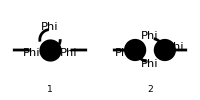

```mathematica
LoopDiags = InsertFields[CreateTopologies[1, 1 -> 1, ExcludeTopologies->{Tadpoles,WFCorrections}],S[1]->S[1], InsertionLevel->{Particles},Model -> FileNameJoin[{NotebookDirectory[],"PhiFour_FA", "PhiFour_FA"}], GenericModel -> FileNameJoin[{NotebookDirectory[],"PhiFour_FA", "PhiFour_FA"}]];
Paint[LoopDiags, Numbering->Simple, SheetHeader->None,ColumnsXRows->{2,1},ImageSize->{200,100}];
AmpLoop[0]=Contract/@FCFAConvert[CreateFeynAmp[LoopDiags,Truncated->True,PreFactor->1],IncomingMomenta->{p},OutgoingMomenta->{p},LoopMomenta->{q},ChangeDimension->D,DropSumOver->True,UndoChiralSplittings->True,SMP->True,FinalSubstitutions->M$FACouplings];
```

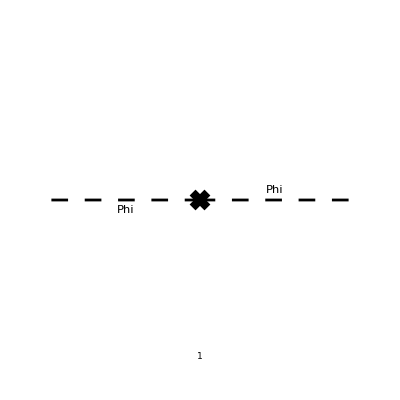

```mathematica
CTDiags = InsertFields[CreateCTTopologies[1, 1 -> 1,ExcludeTopologies->{Tadpoles,WFCorrectionCTs}],S[1]->S[1], InsertionLevel->{Particles}, Model -> FileNameJoin[{NotebookDirectory[],"PhiFour_FA", "PhiFour_FA"}], GenericModel -> FileNameJoin[{NotebookDirectory[],"PhiFour_FA", "PhiFour_FA"}]];
Paint[CTDiags, Numbering->Simple, SheetHeader->None,ColumnsXRows->{2,1},ImageSize->{200,100}];
AmpCT[0]=Contract/@FCFAConvert[CreateFeynAmp[CTDiags,Truncated->True,PreFactor->1],IncomingMomenta->{p},OutgoingMomenta->{p},ChangeDimension->D,DropSumOver->True,UndoChiralSplittings->True,SMP->True,FinalSubstitutions->M$FACouplings];
```

```mathematica
Const1[x_]:=1;
Const0[x_]:=0;
evalLoop[ex_]:=ex//TID[#,q,ToPaVe->True]&//DotSimplify[#,Expanding->False]&//DiracSimplify[#,DiracSubstitute67->True]&//Collect2[#,{A0,B0,C0,D0}]&;
processLoop[exs_]:=(
a1=FCTraceFactor/@DotSimplify[#,Expanding->False]&/@exs;
a2=evalLoop/@a1;
a3=Total[a2];
a4=ChangeDimension[PaXEvaluate[a3],4]//Expand
)
```

```mathematica
AmpLoop[1]=AmpLoop[0]//processLoop;
AmpTotal[0]=(AmpLoop[1]+Total[AmpCT[0]])/ⅈ//Expand;
```

Get::noopen: Cannot open C:\Users\HEP-ph\AppData\Roaming\Mathematica\Applications\X\PacletInfo.m.

Part::partd: Part specification $Failed⟦2⟧ is longer than depth of object.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[2,FeynCalc`PackageX`Private`n1__~~.~~FeynCalc`PackageX`Private`n2__~~.~~FeynCalc`PackageX`Private`n3__:>{FeynCalc`PackageX`Private`n1,FeynCalc`PackageX`Private`n2,FeynCalc`PackageX`Private`n3}].

Identity::argx: Identity called with 2 arguments; 1 argument is expected.

ToExpression::notstrbox: FeynCalc`PackageX`Private`n1__~~.~~FeynCalc`PackageX`Private`n2__~~.~~FeynCalc`PackageX`Private`n3__:>{FeynCalc`PackageX`Private`n1,FeynCalc`PackageX`Private`n2,FeynCalc`PackageX`Private`n3} is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Identity::argx: Identity called with 2 arguments; 1 argument is expected.

```mathematica
RNCond1=Simplify[AmpTotal[0]/.{s->mPhi^2},Assumptions->mPhi>0];
RNCond2=Simplify[D[AmpTotal[0],s]/.{s->mPhi^2},Assumptions->mPhi>0];
RNRes=Solve[{RNCond1==0,RNCond2==0},{FR$delta({mPhi},{}),FR$deltaZ({Phi,Phi},{{}})}]//ComplexExpand;
```

```mathematica
AmpTotal[1]=(AmpTotal[0]/.RNRes[[1]])/.ScaleMu->1//FullSimplify//Expand
```

-(π^3 lambda3^2 s)/(3 √3 mPhi^2)+(π^2 lambda3^2 s)/(2 mPhi^2)+(π^2 lambda3^2 √(s (s-4 mPhi^2)) log((√(s (s-4 mPhi^2))+2 mPhi^2-s)/mPhi^2))/(2 s)-(π^2 lambda3^2 log(2) √(s (s-4 mPhi^2)))/(2 s)+(5 π^3 lambda3^2)/(6 √3)-(π^2 lambda3^2)/2

```mathematica
AmpTotal[2]=AmpTotal[1]/.{mPhi->1,lambda3->0.15};
```

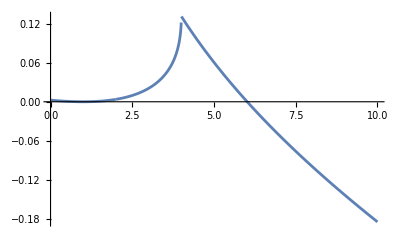

```mathematica
Plot[Re[AmpTotal[2]],{s,0,10}]
```

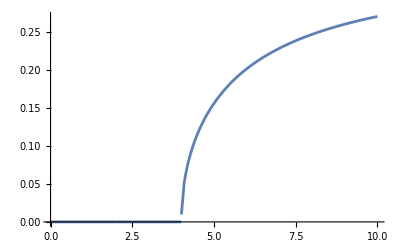

```mathematica
Plot[Im[AmpTotal[2]],{s,0,10}]
```

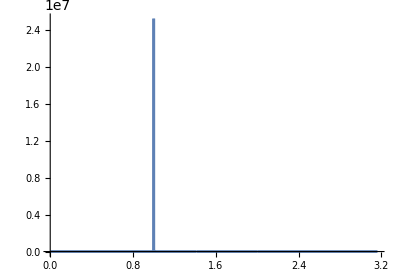

```mathematica
Show[ParametricPlot[{Sqrt[s],Abs[s-1+AmpTotal[2]]^-2},{s,0,10},PlotRange->Full,MaxRecursion->10],AspectRatio->0.7]
```

```mathematica
Series[AmpTotal[1],{s,0,4}]
```

((5 π^3 lambda3^2)/(6 √3)-(3 π^2 lambda3^2)/2)-(((4 √3 π^3-21 π^2) lambda3^2) s)/(36 mPhi^2)+(π^2 lambda3^2 s^2)/(120 mPhi^4)+(π^2 lambda3^2 s^3)/(840 mPhi^6)+(π^2 lambda3^2 s^4)/(5040 mPhi^8)+O(s^(9/2))

```mathematica
Series[1/(s-1+AmpTotal[2]),{s,0,4}]
```

-1.00256-1.00038 s-1.00006 s^2-1.00001 s^3-1. s^4+O(s^(9/2))